```mathematica
mand = Flatten[ImageData@ExampleData[{"TestImage","Mandrill"}],1];
```

```mathematica
mand
```

```mathematica
Dimensions@%
```

{262144,3}

```mathematica
Total@{Total@mand[[1]],Total@mand[[2]],Total@mand[[3]]}
```

2.60392

```mathematica
mand[[1]]
```

{0.643137,0.588235,0.278431}

```mathematica
mand[[2]]
```

{0.247059,0.223529,0.121569}

```mathematica
mand[[3]]
```

{0.294118,0.168627,0.0392157}

```mathematica
ExampleData[{"TestImage", "Mandrill"}] // DominantColors[#, 1][[1]] & // Apply[Plus, #] & (*1-Feedback*)
```

1.07819

```mathematica
ds=ExampleData[{"Dataset","Planets"}];
```

```mathematica
ds[Mean, "Mass"](*2-Feedback*)
```

3.33435×10^26 kg

```mathematica
Mean@ds[[All, 1]]
```

3.33435×10^26 kg

```mathematica
LongestCommonSubsequence[RealDigits[N[GoldenRatio, 10000]] // First, RealDigits[N[Pi, 10000]] // First] // Length(*3-Feedback*)
```

8

```mathematica
Flatten@RealDigits@N[Pi, 10000];
```

```mathematica
Length@LongestCommonSubsequence[Flatten@RealDigits@N[GoldenRatio, 10000],Flatten@RealDigits@N[Pi, 10000]]
```

8

```mathematica
Length@Select[Fibonacci@Range[100],Length[Divisors[#]] == 4 &]
```

19

```mathematica
Select[Divisors[Fibonacci[Range[100]]], Length[#] == 4 &] // Length(*4-Feedback*)
```

19

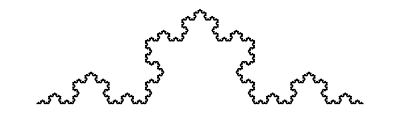

```mathematica
KochCurve[5] // Graphics
```

```mathematica
KochCurve[5] // ArcLength(*5-Feedback*)
```

4.21399

```mathematica
f1 := N[Mean[RandomChoice[Range[1, 100], 100]]];
```

```mathematica
f1 & /@ Range[100000];
```

```mathematica
FindDistribution[%]
```

NormalDistribution[50.4174,3.12638]

```mathematica
FindDistribution[Table[N@Mean[RandomChoice[Range[100], 100]], 10000]](*6-Feedback*)
```

NormalDistribution[50.678,3.0899]

```mathematica
Probability[x^2 + 7 < 8, x \[Distributed] NormalDistribution[]] // N(*7-Feedback*)
```

0.682689

```mathematica
Length@Select[ Range[10000],PrimeQ[#]&&PalindromeQ[#] &]
```

20

```mathematica
Select[Range[10000], (PrimeQ[#] && PalindromeQ[#]) &] // Length(*8-Feedback*)
```

20

```mathematica
oldFaith=ExampleData[{"Statistics","OldFaithful"}][[All,2]];
```

```mathematica
FindDistribution@oldFaith
```

MixtureDistribution[{0.368336,0.631664},{PascalDistribution[32,0.584081],BinomialDistribution[143,0.561364]}]

```mathematica
ibmData = ExampleData[{"Statistics","IBMStockClosingPrices"}];
```

```mathematica
tsm = TimeSeriesModelFit[ibmData]
```

TimeSeriesModel[…]

```mathematica
tsmFe = TimeSeriesModelFit[ExampleData[{"Statistics", "IBMStockClosingPrices"}]](*10-Feedback*)
```

TimeSeriesModel[…]

```mathematica
tsmFe // Normal(*10-Feedback*)
```

ARIMAProcess[-0.279891,{},1,{0.0855756},52.1528]

```mathematica
dateLst = DateRange[DateObject[{2020, 1, 1}], DateObject[{2020, 12, 31}]];
```

```mathematica
MaximalBy[Counts@DayName@dateLst,Identity]
```

<|Wednesday→53,Thursday→53|>

```mathematica
Counts[#["DayName"] & /@DateRange[DateObject[{2020, 1, 1}], DateObject[{2020, 12, 31}]]](*11-Feedback*)
```

<|Wednesday→53,Thursday→53,Friday→52,Saturday→52,Sunday→52,Monday→52,Tuesday→52|>

Syntax::bktmop: Expression "DateRange[DateObject[{2020,1,1}],DateObject[{2020,12,31}]]]" has no opening "[".

```mathematica
img=ColorConvert[ExampleData[{"TestImage","Sailboat"}],"Grayscale"];
```

```mathematica
ReverseSort@Eigenvalues@ImageData@img
```

```mathematica
ImageData[img] // Eigenvalues // ReverseSort // First // Re(*12-Feedback*)
```

243.932

```mathematica
tsm2 = TimeSeriesModelFit@ExampleData[{"Statistics","MinkFurSales"}]
```

TimeSeriesModel[…]

```mathematica
tsmFe2 = TimeSeriesModelFit[ExampleData[{"Statistics", "MinkFurSales"}]];tsmFe2// Normal(*13-Feedback*)
```

ARMAProcess[26060.,{0.499486},{0.318421},2.15638×10^8]

```mathematica
alice=ExampleData[{"Text","OriginOfSpecies"}];
```

```mathematica
sentc = TextSentences@alice;
Length/@TextWords/@sentc
```

```mathematica
Median@%
```

34

```mathematica
Median[Length /@ (TextWords /@ TextSentences[ExampleData[{"Text", "OriginOfSpecies"}]])](*14-Feedback*)
```

34

```mathematica
alce = ExampleData[{"Text","AliceInWonderland"}];
```

```mathematica
origin = ExampleData[{"Text","OriginOfSpecies"}];
```

```mathematica
originText = TextWords@origin;
```

```mathematica
aliceText = TextWords@alce;
```

```mathematica
bothBooks = Join[originText, aliceText];
```

```mathematica
Intersection[TextWords[ExampleData[{"Text", "OriginOfSpecies"}]],
 TextWords[ExampleData[{"Text", "AliceInWonderland"}]]] // Length (*15-Feedback*)
```

907

```mathematica
Select[StringJoin /@ Permutations[{"a", "b", "r", "i", "s", "n"}], DictionaryWordQ](*16-Feedback*)
```

{bairns,brains}

```mathematica
10!(*17-Feedback*)
```

3628800

```mathematica
Permutations[Range[10]] // Length(*17-Feedback*)
```

3628800

Syntax::bktmop: Expression "StringMatchQ[originText[[1]],StartOfString[CharacterRange[A,Z]]]]" has no opening "[".

```mathematica
anagrams[s_String] :=
 Module[{c = Sort[Characters[s]]},
  DictionaryLookup[x__ /; Sort[Characters[x]] == c]]
```

```mathematica
anagrams["abrisn"]
```

{bairns,brains}

```mathematica
Permutations[{1, 2, 3, 4, 5, 6, 7, 8, 9, 10}]
```

```mathematica
Length@anagrams["scrape"]
```

7

```mathematica
Select[StringJoin /@ Permutations[Characters["scrape"]], DictionaryWordQ] // Length (*18-Feedback*)
```

9

```mathematica
Intersection[DictionaryLookup[{"Spanish", "*"}], DictionaryLookup[{"Portuguese", "*"}]] // Length (*19-Feedback*)
```

16365

```mathematica
spanPort = Join[DictionaryLookup[{"Spanish",All}],DictionaryLookup[{"Portuguese",All}]]
```

```mathematica
Length@DictionaryLookup[{"Spanish",All}]
```

86016

```mathematica
Length@DictionaryLookup[{"Portuguese",All}]
```

459996

```mathematica
Length@spanPort
```

546012

```mathematica
dataChicken=ExampleData[{"Statistics","ChickenWeight"}];
```

```mathematica
//TableForm
```

```mathematica
N@Mean@Select[dataChicken, #[[2]]=="horsebean"&][[All, 1]]
```

160.2

```mathematica
N@Mean@Select[dataChicken, #[[2]]=="linseed"&][[All, 1]]
```

218.75

```mathematica
N@Mean@Select[dataChicken, #[[2]]=="soybean"&][[All, 1]]
```

246.429

```mathematica
N@Mean@Select[dataChicken, #[[2]]=="sunflower"&][[All, 1]]
```

328.917

```mathematica
N@Mean@Select[dataChicken, #[[2]]=="meatmeal"&][[All, 1]]
```

276.909

```mathematica
N@Mean@Select[dataChicken, #[[2]]=="casein"&][[All, 1]]
```

323.583

```mathematica
Select[dataChicken, #[[2]]=="sunflower"&][[All, 1]]
```

{423,340,392,339,341,226,320,295,334,322,297,318}

```mathematica
20*70/100
```

14

```mathematica
(70/100 * (25/100)) + (95/100 * (25/100))//N
```

0.4125